### Rogers model and HIREC

```mathematica
WS=w0+Qt b;       (*fitness social learner pre hirec*)
WI=w0+s b-c;   (*fitness individual learner pre hirec*)
Qt=(1-u)((1-p)s+p Qtm1) (*prob of acquiring adaptive behavior recursion*)
```

(p Qtm1+(1-p) s) (1-u)

```mathematica
Solve[{WS==WI,Qt==Qtm1},{p,Qtm1}] (*solve for equilibria for both, phat and qhat*)
```

{{p→(-c+b s u)/(c (-1+u)),Qtm1→(-c+b s)/b}}

```mathematica
phat=(-c+b s u)/(c (-1+u)); (*internal equilibrium of freq social learners*)
qhat = (-c+b s)/b;
```

```mathematica
FullSimplify[phat/(1-phat)]
```

-(c-b s u)/(c u-b s u)

```mathematica
FullSimplify[w0+qhat b] (*internal cultural steady state*)
```

-c+b s+w0

```mathematica
(* post HIREC *)
```

```mathematica
QQt = (1-uu)((1-phat)ss+phat QQtm1);(*recursion post REC*)
```

```mathematica
Simplify[Solve[QQt==QQtm1,QQtm1]] (*solve post REC steady state*)
```

{{QQtm1→-((c-b s) ss u (-1+uu))/(c (u-uu)+b s u (-1+uu))}}

```mathematica
Simplify[-((c-b s) ss u (-1+uu))/(c (u-uu)+b s u (-1+uu))/.{b->B c}](*simplify & replace with B*)
```

((-1+B s) ss u (-1+uu))/(u+B s u (-1+uu)-uu)

```mathematica
hatQQ=((-1+B s) ss u (-1+uu))/(u+B s u (-1+uu)-uu); (*post REC cultural steady state*)
```

```mathematica
hatQ=s-1/B; (*preREC cultural steady state*)
```

```mathematica
Simplify[hatQQ/hatQ] (*BJB unsure what these are doing, ratios of q (freq adaptive behavior) postREC vs. preREC *)
```

(B ss u (-1+uu))/(u+B s u (-1+uu)-uu)

```mathematica
(* fitness difference post-pre HIREC *)
```

```mathematica
Wp=w0+(1-phat)(s b-c)+phat Q b/.Q->s-(c/b); (*Equilib fitness pre REC subbing for B*)
WWp=ww0+(1-phat)(ss bb-cc)+phat QQ bb/.QQ->hatQQ/.B->b/c;
```

```mathematica
Simplify[WWp-Wp]
```

((c-b s)^2 u)/(c (-1+u))-((c-b s) (cc-bb ss) u)/(c (-1+u))-((c-b s) (c-b s u))/(c (-1+u))+(bb (c-b s) ss u (c-b s u) (-1+uu))/(c (-1+u) (c (u-uu)+b s u (-1+uu)))-w0+ww0

```mathematica
Simplify[Solve[WWp-Wp==0,ss]]
```

{{ss→-((c (u-uu)+b s u (-1+uu)) (c^2 (-1+u)+b cc s u-c (b s (-1+u)+cc u+(-1+u) (w0-ww0))))/(bb c (c-b s) (-1+u) u)}}

```mathematica
{{ss->-((c (-1+u)-cc u) (c (u-uu)+b s u (-1+uu)))/(bb c (-1+u) u)}}
```

{{ss→-((c (-1+u)-cc u) (c (u-uu)+b s u (-1+uu)))/(bb c (-1+u) u)}}

```mathematica
Simplify[-((c (u-uu)+b s u (-1+uu)) (c^2 (-1+u)+b cc s u-c (b s (-1+u)+cc u+(-1+u) (w0-ww0))))/(bb c (c-b s) (-1+u) u)/.{bb->b,cc->c}]
```

((c (u-uu)+b s u (-1+uu)) (-c+b s-(-1+u) (w0-ww0)))/(b (-c+b s) (-1+u) u)

```mathematica
FullSimplify[Expand[hatQQ-hatQ]]
```

-((-1+B s) (u+B (s-ss) u (-1+uu)-uu))/(B (u+B s u (-1+uu)-uu))

```mathematica
(* try plotting regions where fitness increases after REC *)
```

```mathematica
?RegionPlot
```

RowBox[{"RegionPlot", "[", RowBox[{StyleBox["pred", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] makes a plot showing the region in which StyleBox["pred", "TI"] is True.

0.9925

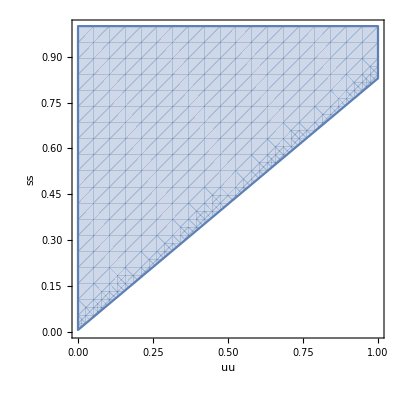

```mathematica
subs={cc->c,bb->b,b-> 2.01,c->1,u->0.1,ss -> s ,s->0.5};
K=WWp-Wp//.subs;
phat/.subs
RegionPlot[K>0,{uu,0,1},{w0,1,1},FrameLabel->{uu,ss}]
```

```mathematica
K=(WWp-Wp)/.{bb->b,cc->c};
Simplify[Reduce[{K>0,s b>c>0,0<u<1,0<uu<1,0<s<1,0<ss<1},Reals],{s b>c>0,0<u<1,0<uu<1,0<s<1,0<ss<1,u s b/c<1}]
```

(u<uu&&((1+ss u==ss+uu&&((b>(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(ss u)/uu≤s<(ss (-1+u))/(-1+uu))||s uu<ss u))||(b>(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(((ss u)/uu<s<(ss (-1+u))/(-1+uu)&&ss+uu<1+ss u)||1+ss u<ss+uu))||(1+ss u<ss+uu&&s uu<ss u)||(ss+uu<1+ss u&&s uu≤ss u)))||(u==uu&&s+ss u<ss+s uu)||(uu<u&&(s+ss u≤ss+s uu||(b<(c (u-uu))/(u (s+ss (-1+u)-s uu))&&(s uu<ss u||ss u≥uu)&&ss+s uu<s+ss u)))

```mathematica
(*lets try changing B hirec and fix s*)
Simplify[WWp-Wp];
Simplify[-((c (-1+u)-cc u) (c (u-uu)+b s u (-1+uu)))/(bb c (-1+u) u)/.{ss->s, cc->c }]

subs={ss->s,cc->c,b-> 4 ,c->1,u->0.01,s->0.9};
K=WWp-Wp//.subs;
phat/.subs
RegionPlot[K>0,{uu,0,1},{bb,1.1,6},FrameLabel->{uu,B}];
```

(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)

0.973737

```mathematica
Simplify[(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)/.{B->b/c, BB->bb/c }]
```

(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)

```mathematica
(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)
Simplify[(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)/.{u->uu }]
```

(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)

(b s)/bb

```mathematica
(c (u-uu)+b s u (-1+uu))/(bb (-1+u) u)
```